```mathematica
deqns={Subscript[m, 1] x1''[t]==(λ1[t]/Subscript[l, 1]) x1[t]-(λ2[t]/Subscript[l, 2])(x2[t]-x1[t]), Subscript[m, 1] y1''[t]==(λ1[t]/Subscript[l, 1]) y1[t]-(λ2[t]/Subscript[l, 2])(y2[t]-y1[t])-Subscript[m, 1] g,
Subscript[m, 2] x2''[t]==(λ2[t]/Subscript[l, 2])(x2[t]-x1[t]),
Subscript[m, 2] y2''[t]==(λ2[t]/Subscript[l, 2]) (y2[t]-y1[t])- Subscript[m, 2] g};


aeqns={x1[t]^2+y1[t]^2==Subscript[l, 1]^2,(x2[t]-x1[t])^2+(y2[t]-y1[t])^2 ==Subscript[l, 2]^2};



params={g->9.81,Subscript[m, 1]->1,Subscript[m, 2]->1,Subscript[l, 1]-> 1,Subscript[l, 2]->1};

(*Escolher A pequeno para visualizar os modos prórprios. Aumentar o valor para observar a transição para o caos*)

A=0.1;
Subscript[θ, 1]=A;
Subscript[θ, 2]=-A*Sqrt[2];

ics={x1[0]==Subscript[l, 1] Sin[Subscript[θ, 1]],y1[0]==-Subscript[l, 1]Cos[Subscript[θ, 1]],y1'[0]==0,x2[0]==Subscript[l, 1] Sin[Subscript[θ, 1]]+Subscript[l, 2] Sin[Subscript[θ, 2]],y2[0]==-Subscript[l, 1]Cos[Subscript[θ, 1]]-Subscript[l, 2] Cos[Subscript[θ, 2]],y2'[0]==0};

soldp=First[NDSolve[{deqns,aeqns,ics}/.params,{x1,y1,x2,y2,λ1,λ2},{t,0,1000},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]];
```

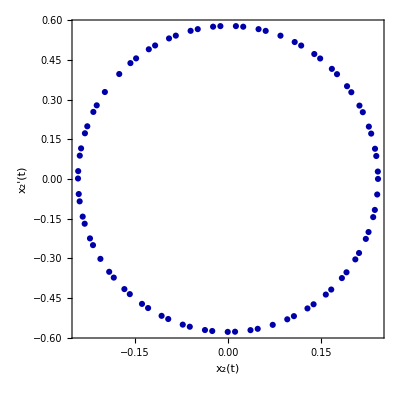

```mathematica
Animate[Graphics[{{PointSize[.025],{Blue,Point[{x1[t],y1[t]}]},{Red, Point[{x2[t],y2[t]}]},Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}]}/. soldp,
{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]} /.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-2.2,2},{-2.5,0.3}}, Axes->True,Ticks->False,ImageSize->500],{t,0,10,0.025},SaveDefinitions->True]

ListPlot[Table[{x2[2π k ],x2'[2π k ]}/.soldp,{k,0,500/(2π)}],AspectRatio->1,PlotStyle->{{Thick,Darker[Blue]}},BaseStyle->{FontFamily->"Times",FontSize->16},FrameStyle->Thickness[0.005],Frame-> True,LabelStyle->{Black},FrameLabel->{"x_2(t)","x_2'(t)"}]
```